```mathematica
d=Daljica[{-1,1},{3,-1}]
```

Daljica[{-1,1},{3,-1}]

```mathematica
Dolzina[Daljica[AA_,BB_]]:=Norm[BB-AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
Slika[Daljica[AA_,BB_]]:=Line[{AA,BB}]
```

```mathematica
Narisi[d_Daljica]:=Graphics[Slika[d]]
```

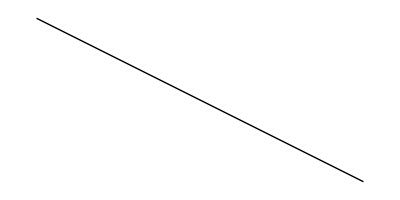

```mathematica
Narisi[d]
```

```mathematica
ClearAll[x,y]
EnacbaNosilke[Daljica[AA_,BB_]]:=Module[{x1,y1,x2,y2,k,n},
{x1,y1}=AA;
{x2,y2}=BB;

k=(y2-y1)/(x2-x1);
n=n/.First[Solve[y1==k*x1+n,n]];
y==k*x+n
]
```

```mathematica
EnacbaNosilke[d]
```

```mathematica
EnacbaNosilke[Daljica[{-1,3},{-4,2}]]
```

y==10/3+x/3

```mathematica
ClearAll[x,y,EnacbaNosilke]
```

```mathematica
bb=Daljica[{-1,3},{-58,215}];
d=Daljica[{-1,1},{3,-1}]
```

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:=Module[{a,b, c,resitev,x1,y1,x2,y2,x3,y3,x4,y4},
a=EnacbaNosilke[d];
b=EnacbaNosilke[bb];
{x1,y1}=AA;
{x2,y2}=BB;
{x3,y3}=CC;
{x4,y4}=DD;
c=x < Max[x1,x2,x3,x4];
resitev=Solve[a && b && c,{x,y}]
 

]
```

```mathematica
Presek[d,bb]
```